```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bret/Documents/PSU Projects/qm619-hw/hw1

(4 Abs[H]^2 Sin[x]^2)/(Ef-Et+ω ℏ)^2

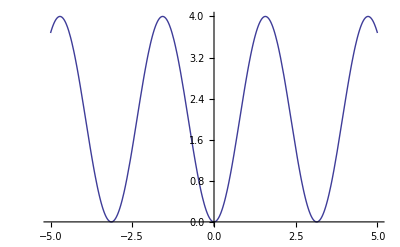

```mathematica
Cf1[t_,x_,ℏ_,Ef_,Et_,ω_,H_]:=4 Abs[H]^2(t/(2ℏ))^2(Sin[x]^2)/(x^2)
Cf1[2 ℏ / (Ef -Et +ℏ ω)x,x,ℏ,Ef,Et,ω,H]
Plot[Cf1[2 ℏ / (Ef -Et +ℏ ω)x,x]/.{H->1,Ef->1,Et->1,ω->1,ℏ->1},{x,-5,5}]
```

```mathematica
Manipulate[Plot[Cf1[2 ℏ / (Ef -Et +ℏ ω)x,x,ℏ,Ef,Et,ω,H],{x,-5,20}],{{ℏ,1},0,5},{{Ef,1},0,5},{{Et,1},0,5},{{ω,1},0,5},{{H,1},0,5}]
```

(4 Abs[H]^2 Sin[x]^2)/(Ef-Et+ω ℏ)^2

```mathematica
Cf1[2 ℏ / (Ef -Et +ℏ ω)x,x]/.{H->1,Ef->1,Et->1,ω->1,ℏ->1}
```

4 Sin[x]^2

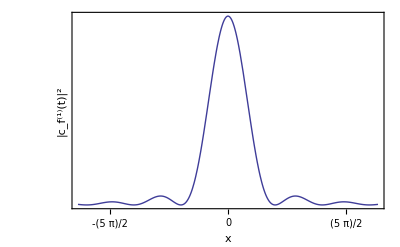

figures/sinc.pdf

```mathematica
Plot[Sin[x]^2/x^2,{x,-10,10},Frame->True, FrameTicks->{Table[π n/(2),{n,-10,10}],None},FrameLabel->{x,"|c_f^(1)(t)|^2"}]
Export["figures/sinc.pdf",%]
```

```mathematica
Plot[Sin[x]^2/x^2,{x,-10,10},Frame->True, FrameTicks->{Table[π n/(2),{n,-10,10}],None},FrameLabel->{x,"|c_f^(1)(t)|^2"}]
```

-Graphics-

```mathematica
Table[π n/(12),{n,1,10}]
```

{π/12,π/6,π/4,π/3,(5 π)/12,π/2,(7 π)/12,(2 π)/3,(3 π)/4,(5 π)/6}

## 3

```mathematica
Integrate[1/(ⅈ ω)D[ⅇ^(ⅈ ω t),t],t]
```

-(ⅈ ⅇ^(ⅈ t ω))/ω

```mathematica
Integrate[1/(ⅈ ω) ⅇ^(ⅈ ω t),{t,0,tp}]
```

(1-ⅇ^(ⅈ tp ω))/ω^2